```mathematica
x=Table[Import[NotebookDirectory[]<>"ticks\\ticks_t5_b10_b0_r"<>ToString@i<>".dat"],{i,51}];
Dimensions@x
```

{51}

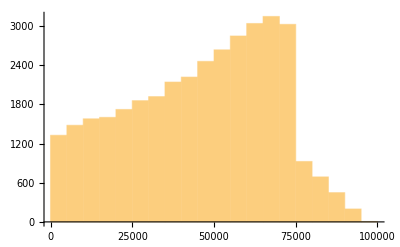

```mathematica
g1=Histogram[Flatten[x[[All,All,1]]]]
```

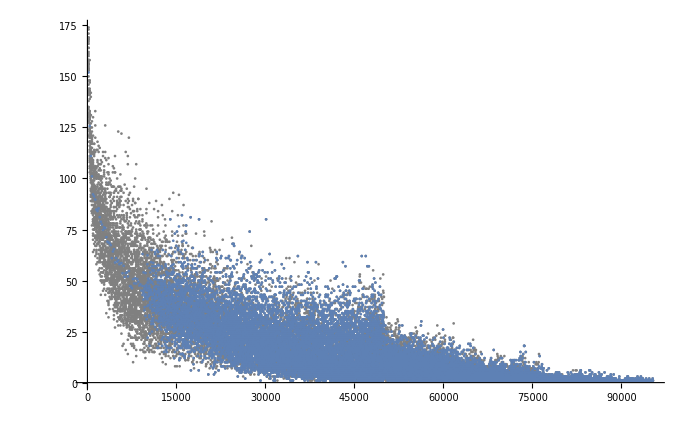

```mathematica
g2=ListPlot[({#[[1]],Total[#[[2;;-1]]]}&/@#)&/@x,Joined->False,PlotRange->All,PlotStyle->Gray];
y=GroupBy[Flatten[({#[[1]],Total[#[[2;;-1]]]}&/@#)&/@x,1],First->Last,Mean];
g3=ListPlot[y,PlotRange->All];
Show@{g2,g3}
```

```mathematica
y=Total[Total[#[[All,2;;-1]]]]&/@x
```

{11147.,11372.,10518.,10433.,12496.,9019.,10902.,15989.,11659.,10559.,12190.,10683.,11990.,11191.,11351.,12044.,10814.,10033.,12855.,11154.,11445.,12411.,13383.,9891.,12725.,13574.,14389.,12524.,11398.,12439.,10549.,11722.,12468.,10779.,14899.,12859.,14105.,16167.,10163.,9735.,11244.,12241.,11808.,10839.,9555.,12386.,13168.,10732.,14497.,11997.,9617.}

```mathematica
Max@y
Mean@y
Min@y
StandardDeviation@y
```

16167.

11845.3

9019.

1583.07